## Free Fermions

```mathematica
Clear[S]
Sv=Table[S[i]=PauliMatrix[i]/2,{i,3}];
```

```mathematica
$Assumptions=Reduce[$Assumptions&&0<=ϕ<2π]
Clear[U,UO]
U[ϕ_]=MatrixExp[ⅈ ϕ S[3]]
```

```mathematica
UO[ϕ_]=Table[Tr[(U[ϕ].S[i].U[ϕ]†//FullSimplify).PauliMatrix[j]]//ExpToTrig,{i,3},{j,3}];
UO[ϕ]//MatrixForm
```

```mathematica
(UO[ϕj]ᵀ.UO[ϕi]//FullSimplify)/.ϕi-ϕj->Δϕ//MatrixForm
```

```mathematica
Svj={xj,yj,zj};
Svjp={xj,yj,0};
Svi={xi,yi,zi};
Svip={xi,yi,0};
```

```mathematica
expr1=Cross[(UO[ϕj].Svj),(UO[ϕi].Svi)][[3]]//FullSimplify;
expr2=Cos[ϕi-ϕj]Cross[Svj,Svi][[3]] + Sin[ϕi-ϕj]Svjp.Svip ;
expr1-expr2//FullSimplify
```

```mathematica
sp=S[1]+ⅈ S[2];
sm=S[1]-ⅈ S[2];
```

```mathematica
S[3]==sp.sm-1/2IdentityMatrix[Dimensions[sp]]
```

```mathematica
Clear[ds]
ds={}
```

```mathematica
L=128;
Clear[h,mzs,denss]
mzs={};
denss={};
hs = Table[h,{h,0.01,2.1,0.0025}];
Monitor[
Do[
s=N[SparseArray[{{i_,i_}->h/2,{i_,j_}/;Abs[i-j]==1->1/2,{i_,j_}/;Abs[i-j]==L-1->0*1/2},{L,L}]];
{vals,vecs}=Eigensystem[s];
order=Ordering[vals];
vals=vals[[order]];
vecs=vecs[[order]]ᵀ;
Nf=First[Position[(#<=10^-12)&/@vals,False]][[1]]-1;
(*Print[Nf];*)
dens=ConstantArray[0,L];
If[Nf>=1,dens=Diagonal[vecs*[[;;,;;Nf]].vecsᵀ[[;;Nf,;;]]];];
mz = dens-ConstantArray[1/2,L];
(*Print[mz];*)
AppendTo[mzs,mz];
AppendTo[denss,dens];
,{h,hs}];,h/2.1]
```

```mathematica
sel=794
denss[[sel]]//Total
ListPlot[mzs[[sel]],Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->MaTeX[{"i","\\langle \\hat S_{z,i} \\rangle"}]]
```

```mathematica
<<MaTeX`
d={hs,Mean[#]&/@mzs}ᵀ;
ds=AppendTo[ds,d];
Manipulate[Show[ListPlot[d[[600;;]],Joined->True,GridLines->{{},{-0.5}},PlotTheme->"Scientific",FrameLabel->MaTeX[{"B_z/J","m_z"}]],Plot[a(2-x)^b-0.5,{x,-2,2},PlotStyle->{Dashed,Black}]],{{a,0.32},0,1},{{b,0.5},0,1}]
```

```mathematica
Show[ListPlot[ds,Joined->True,GridLines->{{},{-0.5}},PlotTheme->"Scientific",FrameLabel->MaTeX[{"B_z/J","m_z"}],PlotLegends->Placed[MaTeX[Table[ToString[2^i],{i,2,Length[ds]}]],{Left,Bottom}]],Plot[0.32(2-x)^0.5-0.5,{x,-2,2},PlotStyle->{Dashed,Black}],PlotRange->{{0,2},{-0.5,-0}}]
```

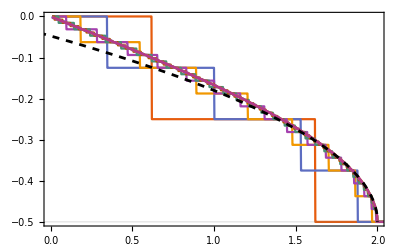

## Spin chain mapping -- check via ED

```mathematica
(* custom Eigensys *)
Clear[myEigensystem]
myEigensystem[H_,nv_:10]:=Module[{vals,vecs,check,order},
{vals,vecs}=Eigensystem[H,nv];
order = Ordering[vals];
vals=vals[[order]];
vecs=vecs[[order]];
vecs=vecsᵀ;

{vals, vecs}
]
$Assumptions=Reduce[$Assumptions&&0<=ϕ<2π];
Clear[U,UO,L,S,B,BO];
U[ϕ_]:=MatrixExp[ⅈ ϕ PauliMatrix[3]/2];
UO[ϕ_]:=Table[Tr[(U[ϕ].PauliMatrix[i].U[ϕ]†//FullSimplify).PauliMatrix[j]]/2//ExpToTrig,{i,3},{j,3}];

L=11;
φ=0.45π;
ϑ=0.5π;
h=0.25;
nv=2^L;nv=20;
pbc=0;

Monitor[Table[S[i,j]=KroneckerProduct[SparseArray[IdentityMatrix[2^(j-1)]],SparseArray[PauliMatrix[i]]/2,SparseArray[IdentityMatrix[2^(L-j)]]],{i,3},{j,L}];,j]
Clear[B,BUO]
$Assumptions=Reduce[$Assumptions&&0<=ϑ<=π/2&&0<=φ<=π/2];

B=SparseArray[{Sin[ϑ],0,Cos[ϑ]}];
BUO[ϕ_]=B.UO[ϕ];

Monitor[ZF=Sum[B[[i]]S[i,x],{x,1,L},{i,3}],x];
Monitor[SZF=Sum[(BUO[x φ])[[i]]S[i,x],{x,1,L},{i,3}];,x]

EXPerpobc = 0*ZF;
Monitor[EXPerpobc+=Sum[S[i,x].S[i,x+1],{x,1,L-1},{i,2}];,x]
EXPerppbc = 0*ZF;
EXPerppbc+=Sum[S[i,L].S[i,1],{i,2}];

ZZobc = 0*ZF;
Monitor[ZZobc+=Sum[S[3,x].S[3,x+1],{x,1,L-1}];,x]
ZZpbc= 0*ZF;
ZZpbc+=S[3,L].S[3,1];

DMobc = 0*ZF;
Monitor[DMobc+=Sum[If[Signature[{3,i,j}]!=0,Signature[{3,i,j}]S[i,x].S[j,x+1],0],{x,1,L-1},{i,3},{j,3}];,x]
DMpbc = 0*ZF;
DMpbc+=Sum[If[Signature[{3,i,j}]!=0,Signature[{3,i,j}]S[i,L].S[j,1],0],{i,3},{j,3}];

Hprime = Cos[φ](EXPerpobc + ZZobc+pbc(EXPerppbc + ZZpbc))+Sin[φ](DMobc+pbc DMpbc)+h ZF;
H = EXPerpobc+pbc EXPerppbc+Cos[φ](ZZobc+pbc ZZpbc) + h SZF;

Monitor[U=Dot[Sequence@@Table[MatrixExp[ⅈ x φ S[3,x]],{x,L}]];,x]
DeleteDuplicates[Chop[Flatten[U.Hprime.U†-H//FullSimplify]]]=={0}

AbsoluteTiming[v1=myEigensystem[-Hprime,nv];]
AbsoluteTiming[v2=myEigensystem[-H,nv];]

v1[[1]]
v2[[1]]

Manipulate[ListPlot[Table[Chop[v1[[2,;;,s]]†.S[i,x].v1[[2,;;,s]]],{i,3},{x,L}],PlotTheme->"Scientific",Joined->True,PlotRange->Full,PlotRangePadding->{0,0.1},PlotLegends->{"x","y","z"}],{s,1,nv,1}]
Manipulate[ListPlot[Table[Chop[v2[[2,;;,s]]†.S[i,x].v2[[2,;;,s]]],{i,3},{x,L}],PlotTheme->"Scientific",Joined->True,PlotRange->Full,PlotRangePadding->{0,0.1},PlotLegends->{"x","y","z"}],{s,1,nv,1}]
```